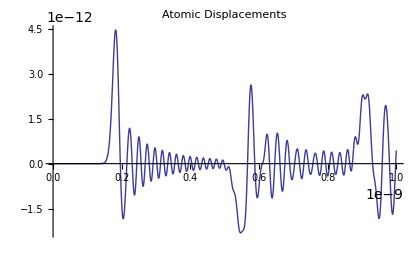
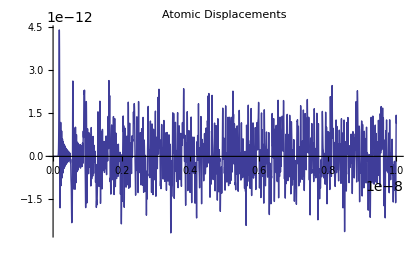

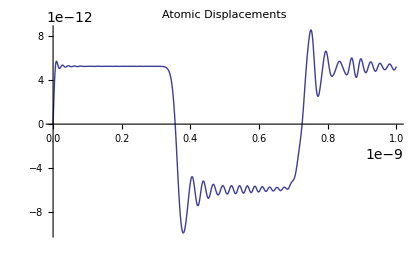

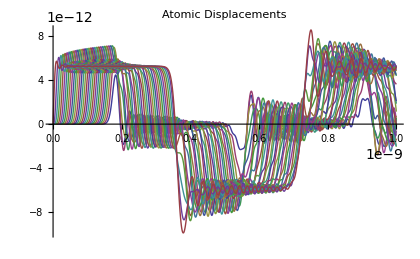

```mathematica
Avagadro=6.022142*10^23;
ze=2.42*10^-10;  (*bond distance 2.42 A in m *)
Ebond=300; (*bond Energy 300 kJ/mol *)
κ=2.55*10^10; (*decay factor in 1/angstrom*)
m1=12/Avagadro; (* weight of One Carbon Atom *) 
IVel=1; (* Initial Velocity of 1DOF model *)
IPos=ze;  (*Initial Position of 1DOF atom *)
endtime=N[10^-8]; (*Simulation End Time*)

(*Formulas And Calculations*)
L=-Ebond*(2*(ze/z)^6-(ze/z)^12); 
V=-Ebond*(2*Exp[-κ*z]-Exp[-2*κ*z]);
(*V=z^2/2;   For test Purposes*)
Va=V/Avagadro;
Fm=D[V,z]/Avagadro;

n=32; (*lattice atoms*)
IPos=ConstantArray[0,n];
IVel=ConstantArray[0,n];  (*Initial Position of 1DOF atom *)
IVel[[n]]=1;

Z=Table[ToExpression[StringJoin["z",ToString[i],"[t]"]],{i,1,n}];

CarbonAtomWeight=N[12/Avagadro];
OxygenAtomWeight=N[16/Avagadro];

MArray=Table[CarbonAtomWeight,{i,1,n}];
M=DiagonalMatrix[MArray];

VPotTemp=Total[Table[Va/.z->(Z[[i]]-Z[[i+1]]),{i,1,n-1}]];
VPot=(Va/.z->Z[[1]])+VPotTemp;


TKin=Sum[0.5*M[[i,i]]*D[Z[[i]],t]^2,{i,1,n}];
Lagrange=TKin-VPot ;

temp1=Table[D[Lagrange,D[Z[[i]],t],t]-D[Lagrange,Z[[i]] ]==0,{i,1,n}];
temp2=Table[{(Z[[i]]/.t->0)==IPos[[i]],(D[Z[[i]],t]/.t->0)==IVel[[i]]},{i,1,n}];

Eqs=Flatten[{temp1,temp2}];


solMDOF=NDSolve[Eqs,Z,{t,0,endtime},MaxSteps->∞,PrecisionGoal->13,AccuracyGoal->13];
Plot[Evaluate[Z[[1]]/.solMDOF],{t,0,endtime},PlotRange->All,PlotLabel->"Atomic Displacements",ImageSize->420]Plot[Evaluate[Z[[1]]/.solMDOF],{t,0,endtime/10},PlotRange->All,PlotLabel->"Atomic Displacements",ImageSize->420]
Plot[Evaluate[Z[[n]]/.solMDOF],{t,0,endtime/10},PlotRange->All,PlotLabel->"Atomic Displacements",ImageSize->420]
Plot[Evaluate[Z/.solMDOF],{t,0,endtime/10},PlotRange->All,PlotLabel->"Atomic Displacements",ImageSize->420]
```